# 常用算法

## 1、求解代数方程组

求解多项式方程组

```mathematica
Solve[x^3-x+1==0,x](*低于5次的给出解析解*)
```

{{x→-(2/(3 (9-√69)))^(1/3)-(1/2 (9-√69))^(1/3)/3^(2/3)},{x→((1+ⅈ √3) (1/2 (9-√69))^(1/3))/(2 3^(2/3))+(1-ⅈ √3)/(2^(2/3) (3 (9-√69))^(1/3))},{x→((1-ⅈ √3) (1/2 (9-√69))^(1/3))/(2 3^(2/3))+(1+ⅈ √3)/(2^(2/3) (3 (9-√69))^(1/3))}}

```mathematica
NSolve[x^3-x+1==0,x](*数值解*)
Solve[x^3-x+1==0,x]//N
```

{{x→-1.32472},{x→0.662359-0.56228 ⅈ},{x→0.662359+0.56228 ⅈ}}

{{x→-1.32472},{x→0.662359-0.56228 ⅈ},{x→0.662359+0.56228 ⅈ}}

```mathematica
Solve[x^6-x+1==0,x](*高于5次的一般给出解析解*)
Solve[x^6-x+1==0,x]//N
NSolve[x^6-x+1==0,x]
```

{{x→Root[1-#1+#1^6&,1]},{x→Root[1-#1+#1^6&,2]},{x→Root[1-#1+#1^6&,3]},{x→Root[1-#1+#1^6&,4]},{x→Root[1-#1+#1^6&,5]},{x→Root[1-#1+#1^6&,6]}}

{{x→-0.945402-0.611837 ⅈ},{x→-0.945402+0.611837 ⅈ},{x→0.154735-1.03838 ⅈ},{x→0.154735+1.03838 ⅈ},{x→0.790667-0.300507 ⅈ},{x→0.790667+0.300507 ⅈ}}

{{x→-0.945402-0.611837 ⅈ},{x→-0.945402+0.611837 ⅈ},{x→0.154735-1.03838 ⅈ},{x→0.154735+1.03838 ⅈ},{x→0.790667-0.300507 ⅈ},{x→0.790667+0.300507 ⅈ}}

求解超越性代数方程

```mathematica
Solve[Sin[x]+x+5==0,x](*超越方程*)
NSolve[Sin[x]+x+5==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[5+x+Sin[x]==0,x]

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[5+x+Sin[x]==0,x]

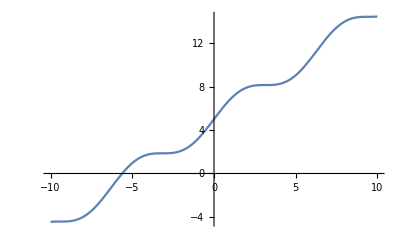

```mathematica
Plot[Sin[x]+x+5,{x,-10,10}]
```

```mathematica
FindRoot[Sin[x]+x+5==0,{x,1}]
FindRoot[Sin[x]+x+5==0,{x,1,2}]
FindRoot[Sin[x]+x+5==0,{x,1.5,1,2}]
FindRoot[Sin[x]+x+5==0,{x,-5.5,-10,-2}]
```

{x→-5.61756}

{x→-5.61756}

FindRoot::reged: The point {1.} is at the edge of the search region {1., 2.} in coordinate 1 and the computed search direction points outside the region.

{x→1.}

{x→-5.61756}

## 更多细节

### 1、牛顿法

while |x_k-x_(k-1)|<ϵ or |(x_k-x_(k-1))/x_k|<ϵ
	x_(k+1)=x_k-(f(x_k))/(f'(x_k))

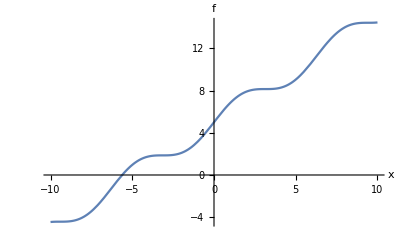

x=-5.61756 k=7

```mathematica
f[x_]:=Sin[x]+x+5;
Plot[f[x],{x,-10,10},AxesLabel->{"x","f"}]
ϵ=10^-6;k=0;x1=-1;x2=-1.2;
While[Abs[(x2-x1)/x2]>ϵ ∨Abs[x2-x1]>ϵ,
temp=x2;x2=x2-f[x2]/(Evaluate[D[f[x],x]]/.x->x2);
x1=temp;k++]
Print["x=",x2," k=",k]
Clear["Global`*"]
```

```mathematica
f[x_]:=Sin[x]+x+5;ϵ=10^-6;k=0;x1=-1;x2=-1.2;
Timing[While[Abs[(x2-x1)/x2]>ϵ ∨Abs[x2-x1]>ϵ,
temp=x2;x2=x2-f[x2]/(Evaluate[D[f[x],x]]/.x->x2);
x1=temp;k++]]
Clear["Global`*"]
```

{0.00022,Null}

### 2、牛顿法的改进——割线法（更快）

while |x_k-x_(k-1)|<ϵ or |(x_k-x_(k-1))/x_k|<ϵ
	x_(k+1)=x_k-(f(x_k))/(f(x_k)-f(x_(k-1)))(x_k-x_(k-1))

```mathematica
f[x_]:=Sin[x]+x+5;
Plot[f[x],{x,-10,10},AxesLabel->{"x","f"}]
ϵ=10^-6;k=0;x1=-1;x2=-1.2;
While[Abs[(x2-x1)/x2]>ϵ ∨Abs[x2-x1]>ϵ,
temp=x2;x2=x2-f[x2]/(f[x2]-f[x1]) (x2-x1);
x1=temp;k++]
Print["x=",x2," k=",k]
Clear["Global`*"]
```

-Graphics-

x=-5.61756 k=9

```mathematica
f[x_]:=Sin[x]+x+5;ϵ=10^-6;k=0;x1=-1;x2=-1.2;Timing[While[Abs[(x2-x1)/x2]>ϵ ∨Abs[x2-x1]>ϵ,
temp=x2;x2=x2-f[x2]/(f[x2]-f[x1]) (x2-x1);
x1=temp;k++]]
Clear["Global`*"]
```

{0.0002,Null}

多元超越代数方程

先线性化方程组
f1(x0,y0)+f_(1x)'(x0,y0)(x-x0)+f_(1y)'(x0,y0)(y-y0)=0
f2(x0,y0)+f_(2x)'(x0,y0)(x-x0)+f_(2y)'(x0,y0)(y-y0)=0
再迭代求解(用NSolve,x0→s[[1]],y0→s[[2]])至期望精度

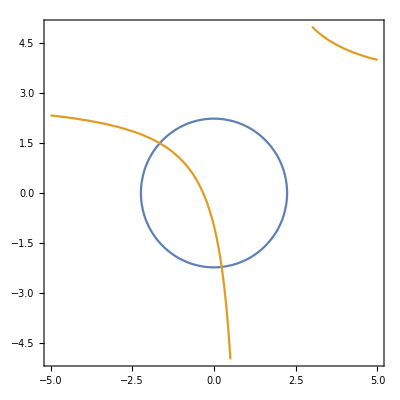

```mathematica
f1[x_,y_]:=x^2+y^2-5;
f2[x_,y_]:=(x-1) y-(3 x+1);
ContourPlot[{f1[x,y]==0,f2[x,y]==0},{x,-5,5},{y,-5,5}]
Clear["Global`*"]
```

```mathematica
f1[x_,y_]:=x^2+y^2-5;
f2[x_,y_]:=(x-1) y-(3 x+1);
df1[x_,y_]:=Evaluate[{D[f1[x,y],x],D[f1[x,y],y]}];
df2[x_,y_]:=Evaluate[{D[f2[x,y],x],D[f2[x,y],y]}];
equs={f1[x0,y0]+df1[x0,y0][[1]](x-x0)+df1[x0,y0][[2]](y-y0)==0,f2[x0,y0]+df2[x0,y0][[1]](x-x0)+df2[x0,y0][[2]](y-y0)==0};
{x1,y1}={-2,2};ϵ=10^-6;k=0;While[s=NSolve[equs/.{x0->x1,y0->y1},{x,y}];{x2,y2}={x,y}/.s[[1]];Abs[x2-x1]>ϵ∨Abs[y2-y1]>ϵ,{x1,y1}={x2,y2};k++]
Print["x=",x1," y=",y1," k=",k]
Clear["Global`*"]
```

x=-1.66113 y=1.49688 k=3

直接用FindRoot求解

```mathematica
f1[x_,y_]:=x^2+y^2-5;
f2[x_,y_]:=(x-1) y-(3 x+1);
FindRoot[{f1[x,y]==0,f2[x,y]==0},{{x,-2},{y,2}}]
FindRoot[{f1[x,y]==0,f2[x,y]==0},{{x,0},{y,-2}}]
Clear["Global`*"]
```

{x→-1.66113,y→1.49688}

{x→0.234268,y→-2.22376}

## 2、求函数极值

一元函数求极值

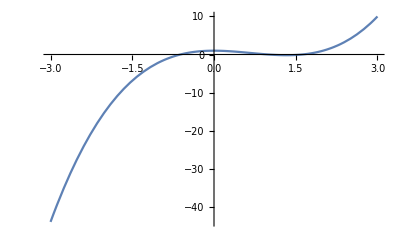

```mathematica
f[x_]:=x^3-2 x^2+1;
Plot[f[x],{x,-3,3}]
Clear["Global`*"]
```

```mathematica
f[x_]:=x^3-2 x^2+1;
FindMinimum[f[x],{x,1}]
Clear["Global`*"]
```

{-0.185185,{x→1.33333}}

## 更多细节

### 1、普通解法——导数为0

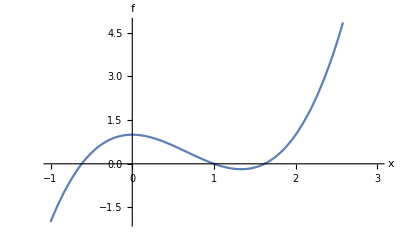

{{x→0},{x→4/3}}

```mathematica
f[x_]:=x^3-2 x^2+1;
Plot[f[x],{x,-1,3},AxesLabel->{"x","f"}]
df[x_]:=Evaluate[-D[f[x],x]];
Solve[df[x]==0,x]
```

### 2、最速下降法

-Graphics-

{k,x,f[x]}={1000,1.33333,-0.185185}

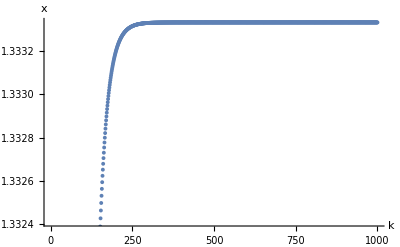

```mathematica
f[x_]:=x^3-2 x^2+1;
Plot[f[x],{x,-1,3},AxesLabel->{"x","f"}]
df[x_]:=Evaluate[-D[f[x],x]];
α=0.01;ϵ=10^-5;n=10^3;(*α为步长，ϵ为精度，n为最大迭代次数*)
x=1;k=0;data={};
While[Abs[df[x]]>ϵ∨k<n,
AppendTo[data,x];x=x+α df[x];k++]
Print["{k,x,f[x]}=",{k,x,f[x]}]
ListPlot[data,AxesLabel->{"k","x"}]
Clear["Global`*"]
```

### 3、黄金率搜索法

优点：不需要求导数；
缺点：必须给出搜索区间，并且在区间中函数为单谷的

```mathematica
f[x_]:=x^3-2 x^2+1;
a=0;b=2;
ϵ=10^-6;γ=1/GoldenRatio//N;k=0;
x1=a+γ (b-a);x2=a+γ^2(b-a);
u=f[x1];v=f[x2];
While[Abs[a-b]>ϵ,
If[u>v,
b=x1;x1=x2;u=v;v=f[x2=a+γ^2(b-a)],
a=x2;x2=x1;v=u;u=f[x1=a+γ(b-a)]];
k++]
x=(a+b)/2;
Print["k=",k," x=",x," f[x]=",f[x]]
Clear["Global`*"]
```

k=31 x=1.33333 f[x]=-0.185185

多元函数求极值

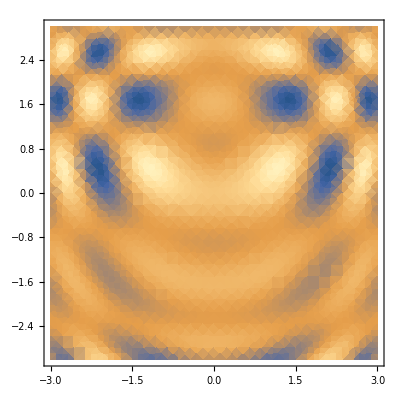

```mathematica
f[x_]:=Cos[x[[1]]^2-3 x[[2]]]+Sin[x[[1]]^2+x[[2]]^2];
DensityPlot[f[{x,y}],{x,-3,3},{y,-3,3}](*先利用密度图函数观察极值点大概位置*)
```

```mathematica
(*发现有一个极值点在在｛－2，0｝附近*)
x0={-2,-0.5};FindMinimum[f[{x,y}],{{x,x0[[1]]},{y,x0[[2]]}}]
Clear["Global`*"]
```

{-2.,{x→-2.12265,y→0.454686}}

## 更多细节

### 1、最速下降法

```mathematica
f[x_]:=Cos[x[[1]]^2-3 x[[2]]]+Sin[x[[1]]^2+x[[2]]^2];
DensityPlot[f[{x,y}],{x,-3,3},{y,-3,3}](*先利用密度图函数观察极值点大概位置*)
Clear["Global`*"]
```

-Graphics-

Part::partd: Part specification x ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification x ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification x ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

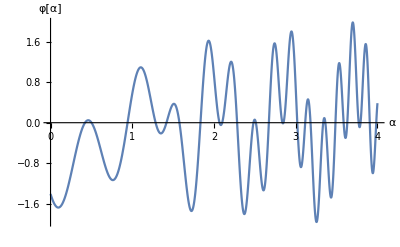

```mathematica
(*发现有一个极值点在在｛－2，0｝附近*)
(*观察φ[α]的极值点的α，为最适合的步长*)
f[x_]:=Cos[x[[1]]^2-3 x[[2]]]+Sin[x[[1]]^2+x[[2]]^2];df[x_]:=Evaluate[{-D[f[x],x[[1]]],-D[f[x],x[[2]]]}];
x0={-2,0};φ[α_]:=f[x0+α df[x0]];
Plot[φ[α],{α,0,4},PlotRange->All,AxesLabel->{"α","φ[α]"}]
Clear["Global`*"]
```

Part::partd: Part specification x ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification x ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification x ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

k=35 x={-2.12265,0.454685} f[x]=-2.

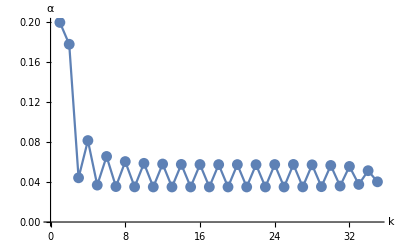

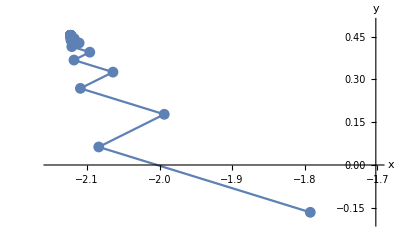

```mathematica
(*为方便定一个极值点在在｛－2，-0.5｝附近*)
f[x_]:=Cos[x[[1]]^2-3 x[[2]]]+Sin[x[[1]]^2+x[[2]]^2];df[x_]:=Evaluate[{-D[f[x],x[[1]]],-D[f[x],x[[2]]]}];
x0={-2,-0.5};
ϵ1=10^-10;k=0;datax=dataα={};
ϵ2=10^-4;γ=1/GoldenRatio//N;
While[df[x0].df[x0]>ϵ1,
(*整个在循环寻找f[x]的极值点*)

(*搜索α第一个极小值所在区间*)
α=0;δ=0.1;g=0;
While[g==0;
if[f[x0+α df[x0]]>f[x0+(α+δ)df[x0]],α=α+δ,g=1]];
a=α-δ;b=α+δ;

(*用黄金率搜索法搜索α的第一个极小值*)
φ[α_]:=f[x0+α df[x0]];
θ1=a+γ(b-a);θ2=a+γ^2(b-a);
u=φ[θ1];v=φ[θ2];
While[Abs[a-b]>ϵ2,
If[u>v,
b=θ1;θ1=θ2;u=v;v=φ[θ2=a+γ^2(b-a)],
a=θ2;θ2=θ1;v=u;u=φ[θ1=a+γ(b-a)]]];
α=(a+b)/2;

(*记录α和x的值*)
x0=x0+α df[x0];k++;
AppendTo[dataα,α];AppendTo[datax,x0]
]

(*输出寻找到极值点*)
Print["k=",k," x=",x0," f[x]=",f[x0]]
ListLinePlot[dataα,Mesh->Full,PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"k","α"}]
ListLinePlot[datax,Mesh->Full,AxesLabel->{"x","y"},PlotRange->{{-2.15,-1.7},{-0.2,0.5}}]
Clear["Global`*"]
```

## 3、求解线性方程组

严格解

### 1、用Solve解（直观）

```mathematica
(*随机创建一个5元线性方程组*)
n=5;i=IdentityMatrix[n];X=Array[x,n];
A=RandomInteger[{-3,3},{n,n}];
B=RandomInteger[{-5,5},n];
Print[A//MatrixForm,X//MatrixForm," = ",B//MatrixForm]
(*用Solve解矩阵形式方程*)
s=Solve[Thread[A.X==B],X];
Print["X= ",X/.s[[1]]//MatrixForm]
A.(X/.s[[1]])==B
Clear["Global`*"]
```

(3 | 3 | 2 | 2 | 0
-1 | -1 | 3 | -3 | 1
1 | 0 | -1 | 0 | 0
3 | 0 | 2 | -2 | -2
-2 | 1 | 1 | 0 | -2)(x[1]
x[2]
x[3]
x[4]
x[5]) = (3
-1
4
-3
-4)

X= (9/26
317/52
-95/26
-469/104
23/8)

True

### 2、用LinearSolve解（超快速）

```mathematica
(*随机创建一个5元线性方程组*)
n=5;i=IdentityMatrix[n];X=Array[x,n];
A=RandomInteger[{-3,3},{n,n}];
B=RandomInteger[{-5,5},n];
Print[A//MatrixForm,X//MatrixForm," = ",B//MatrixForm]
(*用LinearSolve解矩阵形式方程*)
s=LinearSolve[A,B];
Print["X= ", X/.X-> s//MatrixForm]
A.(X/.X-> s)==B
Clear["Global`*"]
```

(0 | 3 | 3 | 0 | 3
2 | 1 | -2 | -1 | -1
0 | 1 | -2 | -2 | -2
0 | 1 | -2 | 0 | -2
-3 | -2 | 0 | -1 | -3)(x[1]
x[2]
x[3]
x[4]
x[5]) = (3
4
-2
-2
-2)

X= (16/3
0
17/3
0
-14/3)

True

### 3、LinearSolve和直接求逆法比较

```mathematica
n=6000;
m=RandomReal[{-3,6},{n,n}];
b=RandomReal[{-10,20},n];
{time,res}=Timing[LinearSolve[m,b]];
Print["Time of LinearSolve =",time]
{time,res}=Timing[Inverse[m].b];
Print["Time of Inverse =",time]
Clear["Global`*"]
```

Time of LinearSolve =6.08819

Time of Inverse =16.4039

### 4、Solve的时间复杂度

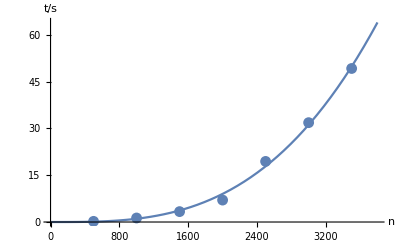

s=-1.7×10^-7 n^2+1.21×10^-9 n^3

```mathematica
data={};
Do[
X=Array[x,n];
c=RandomInteger[{-1,1},{n,n}];
b=RandomReal[{-3,3},n];
equ=Thread[c.X==b];
{t,r}=Timing[Solve[equ,X]];
AppendTo[data,{n,t}],
{n,500,3500,500}]
s=Fit[data,{n^2,n^3},n];
g1=Plot[s,{n,0,3800}];
g2=ListPlot[data];
Show[{g1,g2},PlotRange->All,AxesLabel->{"n","t/s"}]
Print["s=",s]
Clear["Global`*"]
```

### 5、LinearSolve的时间复杂度(远快于Solve)

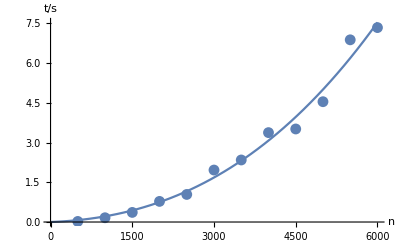

s=0.00008 n+1.×10^-7 n^2+1.×10^-11 n^3

```mathematica
data={};
Do[
X=Array[x,n];
c=RandomInteger[{-1,1},{n,n}];
b=RandomReal[{-3,3},n];
{t,r}=Timing[LinearSolve[c,b]];
AppendTo[data,{n,t}],
{n,500,6000,500}]
s=Fit[data,{n^2,n^3,n},n];
g1=Plot[s,{n,0,6000}];
g2=ListPlot[data];
Show[{g1,g2},PlotRange->All,AxesLabel->{"n","t/s"}]
Print["s=",s]
Clear["Global`*"]
```

## 更多细节

### 1、利用LU分解法计算——手工

```mathematica
(*随机创建一个5元线性方程组*)
n=5;i=IdentityMatrix[n];X=Array[x,n];
A=RandomInteger[{-3,3},{n,n}];
B=RandomInteger[{-5,5},n];
Print[A//MatrixForm,X//MatrixForm," = ",B//MatrixForm]
(*LU分解法演示*)
Do[
list=Table[A[[i,k]],{i,k,n}];(*此处的i已经被局部变量覆盖*)
q=Position[Abs[list],Max[Abs[list]]][[1,1]];
P=i;(*此处的i恢复原值——矩阵*)
{P[[k]],P[[q+k-1]]}={P[[q+k-1]],P[[k]]};
A=P.A;B=P.B;L=i;
Do[L[[i,k]]=-A[[i,k]]/A[[k,k]],{i,k+1,n}];(*此处的i已经被局部变量覆盖*)
A=L.A;B=L.B,
{k,n-1}]
x0={B[[n]]/A[[n,n]]};
Do[PrependTo[x0,
(B[[k]]-Sum[A[[k,k+i]]x0[[i]],{i,n-k}])/A[[k,k]]],
{k,n-1,1,-1}]
Print["X=",x0//MatrixForm]
A.(x0)==B
Clear["Global`*"]
```

(2 | -3 | 2 | -3 | -1
3 | 0 | 0 | -3 | 3
3 | -1 | 3 | 2 | -3
3 | -1 | -2 | -2 | 0
1 | 2 | 1 | 3 | -3)(x[1]
x[2]
x[3]
x[4]
x[5]) = (5
1
4
5
3)

X=(409/480
209/480
-67/240
-557/480
-403/240)

True

### 2、利用LU分解法计算——LUDecomposition

```mathematica
(*随机创建一个5元线性方程组*)
n=5;q=IdentityMatrix[n];X0=Array[x,n];
A=RandomInteger[{-3,3},{n,n}];
B=RandomInteger[{-5,5},n];
Print[A//MatrixForm,X0//MatrixForm," = ",B//MatrixForm]

{lu,v,c}=LUDecomposition[A];
L=lu SparseArray[{i_,j_}/;j<i->1,{n,n}]+q;
U=lu SparseArray[{i_,j_}/;j≥i->1,{n,n}];
P=Table[q[[v[[i]]]],{i,n}];
B=P.B;

Y={B[[1]]};
Do[
AppendTo[Y,B[[k]]-Sum[L[[k,i]] Y[[i]],{i,k-1}]],{k,2,n}]

X={Y[[n]]/U[[n,n]]};
Do[
PrependTo[X,
(Y[[k]]-Sum[U[[k,k+i]]X[[i]],{i,n-k}])/U[[k,k]]],
{k,n-1,1,-1}]
Print[X0//MatrixForm,"=",X//MatrixForm]
Clear["Global`*"]
```

(-1 | 3 | 1 | 0 | -1
-1 | 1 | -1 | 3 | -2
2 | 0 | -3 | 3 | 0
1 | 3 | 2 | -3 | 3
3 | 0 | -1 | 1 | 2)(x[1]
x[2]
x[3]
x[4]
x[5]) = (-3
4
4
1
5)

(x[1]
x[2]
x[3]
x[4]
x[5])=(-83/23
-11/23
20/23
106/23
139/23)

近似解

## 更多细节

### 1、经典迭代法 （＊未完＊）

### 2、Krylov子空间方法 （＊未完＊）

## 4、求解常微分方程

初值问题

微分方程的一般形式可以写成
f[t, x1, x1', x2, x2', ...] == 0
而多元或高阶微分方程可以拆分成一阶导数的方程组

一阶微分方程可以写成
x'[t] == f[t, x[t]]
初值问题是 : 给定t＝0时的x值x0，如何求解t > 0 时的x[t]?

### 1、一阶方程的初值问题

{{x→Function[{t},ⅇ^-t]}}

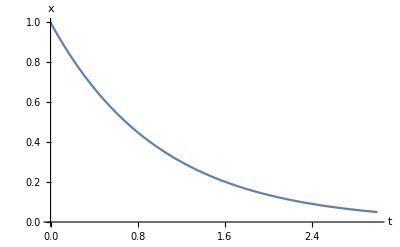

```mathematica
DSolve[{x'[t]+x[t]==0,x[0]==1},x,t]
Plot[x[t]/.%[[1]],{t,0,3},AxesLabel->{"t","x"}]
```

```mathematica
NDSolve[{x'[t]+x[t]==0,x[0]==1},x,{t,0,3}]
Plot[x[t]/.%,{t,0,3},AxesLabel->{"t","x"}]
```

{{x→InterpolatingFunction[{{0., 3.}}, <>]}}

-Graphics-

### 2、二阶方程的初值问题

{{x→Function[{t},Cos[t]]}}

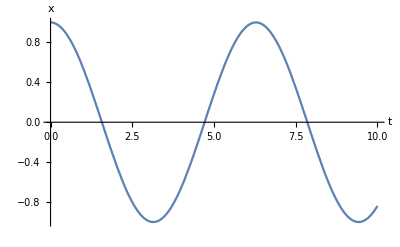

```mathematica
DSolve[{x''[t]+x[t]==0,x[0]==1,x'[0]==0},x,t]
Plot[x[t]/.%[[1]],{t,0,10},AxesLabel->{"t","x"}]
```

```mathematica
NDSolve[{x''[t]+x[t]==0,x[0]==1,x'[0]==0},x,{t,0,10}]
Plot[x[t]/.%,{t,0,10},AxesLabel->{"t","x"}]
```

{{x→InterpolatingFunction[{{0., 10.}}, <>]}}

-Graphics-

## 更多细节

### 1、Euler法

一阶微分方程可以写成
x'[t] == f[t, x[t]]
初值问题是 : 给定t＝0时的x值x0，如何求解t > 0 时的x[t]?

将自变量t划分为许多小等间隔区间，区间的分点表示为t0, t1, t2, t3, ... 间隔为δt
而用差分代替导数，则有
(x_(i+1)-x_i)/δt==f[t_i,x_i],i=1,2,3,...
其中x_i=x[t_i]
于是x_(i＋1)==x_i+δt×f[t_i,x_i]
由此递推即可得到各个分点的x值

之后还可进行插值操作，即在两点之间寻找一个函数使得两点光滑连接
用Interpolation[list, InterpolationOrder -> n] 命令

{{0,1}}

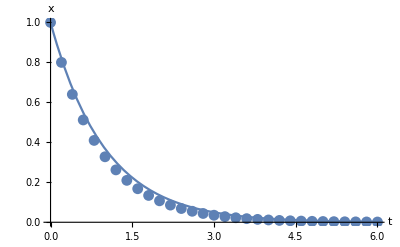

```mathematica
δt=2.0*10^-1;n=3*10;
f[t_,x_]:=-x;
x0=1;
data={{0,x0}}
Do[
AppendTo[data,{i δt,data[[-1,2]]+δt f[data[[-1,1]],data[[-1,2]]]}],{i,n}](*data[[-1]]代表选取倒数第二个元素*)
g1=ListPlot[data];
g2=Plot[ⅇ^-t,{t,0,n δt},PlotRange->All];
Show[{g1,g2},AxesLabel->{"t","x"},PlotRange->All]
Clear["Global`*"]
```

对于高阶微分方程需要联立成多个一阶方程
对于x’’[t]+x[t]==0,x[0]==1,x’[0]==0
拆分成
 x1’=x2
 x2’=-x1
(其中x1=x)

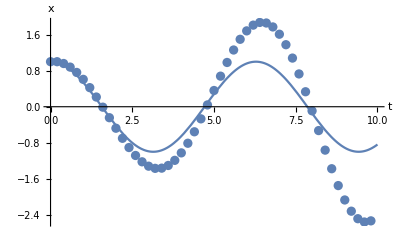

```mathematica
n=5*10;δt=2*10^-1;
f[t_,x_]:={x[[2]],-x[[1]]};
x0={1,0};data={x0};
Do[
AppendTo[data,data[[-1]]+δt f[(i-1) δt,data[[-1]]]],{i,n}]
(*data[[_,1]]为x数据，data[[_,2]]为x'数据*)
data=Table[{(i-1) δt,data[[i,1]]},{i,n}];
g1=ListPlot[data];
g2=Plot[Cos[t],{t,0,n δt},PlotRange->All];
Show[{g1,g2},AxesLabel->{"t","x"},PlotRange->All]
Clear["Global`*"]
```

### 2、预估－校正法——Euler法的改进

由x'[t] == f[t, x[t]]可以得到积分
x_(i+1)=x_i+∫_t_i^(t_(i+1)) f[τ,x[τ]]ⅆτ
用梯形面积近似
x_(i+1)=x_i+1/2 δt×[f[t_i,x_i]+f[t_(i+1),x_(i+1)]]为一隐式方程
进一步近似，(即用Euler法求出近似的x_(i+1))^*:
(x_(i+1))^*=x_i+δt×f[t_i,x_i]
再带入梯形公式求出更好的x_(i+1):
x_(i+1)=x_i+1/2 δt×[f[t_i,x_i]+f[t_(i+1),(x_(i+1))^*]]

{{0,1}}

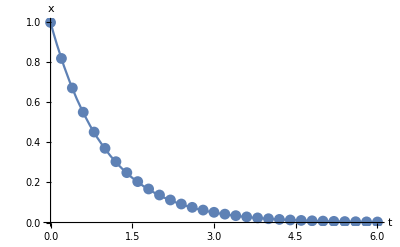

```mathematica
δt=2.0*10^-1;n=3*10;
f[t_,x_]:=-x;
x0=1;
data={{0,x0}}
Do[
SuperStar[x]=data[[-1,2]]+δt f[data[[-1,1]],data[[-1,2]]];
AppendTo[data,{i δt,data[[-1,2]]+1/2 δt(f[data[[-1,1]],data[[-1,2]]]+f[data[[-1,1]]+δt,SuperStar[x]])}],{i,n}]
g1=ListPlot[data];
g2=Plot[ⅇ^-t,{t,0,n δt},PlotRange->All];
Show[{g1,g2},AxesLabel->{"t","x"},PlotRange->All]
Clear["Global`*"]
```

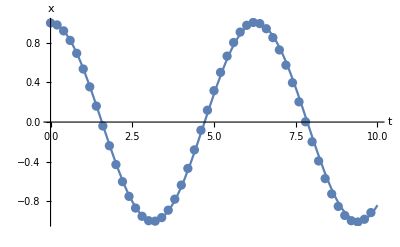

```mathematica
n=5*10;δt=2*10^-1;
f[t_,x_]:={x[[2]],-x[[1]]};
x0={1,0};data={x0};
Do[
SuperStar[x]=data[[-1]]+δt f[(i-1)δt,data[[-1]]];
AppendTo[data,data[[-1]]+1/2 δt( f[(i-1) δt,data[[-1]]]+f[i δt,SuperStar[x]])],{i,n}]
(*data[[_,1]]为x数据，data[[_,2]]为x'数据*)
data=Table[{(i-1) δt,data[[i,1]]},{i,n}];
g1=ListPlot[data];
g2=Plot[Cos[t],{t,0,n δt},PlotRange->All];
Show[{g1,g2},AxesLabel->{"t","x"},PlotRange->All]
Clear["Global`*"]
```

### 3、4阶Runge-Kutta法——更进一步的改进

x_(i+1)=x_i+1/6(k1+2k2+2k3+k4);
k1=δt×f[t_i,x_i];
k2=δt×f[t_i+δt/2,x_i+k1/2];
k3=δt×f[t_i+δt/2,x_i+k2/2];
k4=δt×f[t_i+δt,x_i+k3];

{{0,1}}

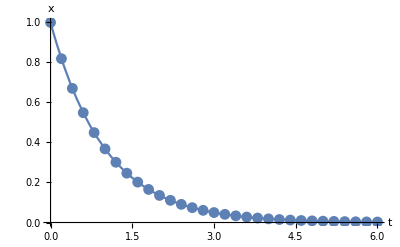

```mathematica
δt=2.0*10^-1;n=3*10;
f[t_,x_]:=-x;
x0=1;
data={{0,x0}}
Do[
k1=δt f[data[[-1,1]],data[[-1,2]]];
k2=δt f[data[[-1,1]]+1/2 δt,data[[-1,2]]+k1/2];
k3=δt f[data[[-1,1]]+1/2 δt,data[[-1,2]]+k2/2];
k4=δt f[data[[-1,1]]+δt,data[[-1,2]]+k3];
AppendTo[data,{i δt,data[[-1,2]]+1/6(k1+2 k2+2 k3+k4)}],{i,n}]
g1=ListPlot[data];
g2=Plot[ⅇ^-t,{t,0,n δt},PlotRange->All];
Show[{g1,g2},AxesLabel->{"t","x"},PlotRange->All]
Clear["Global`*"]
```

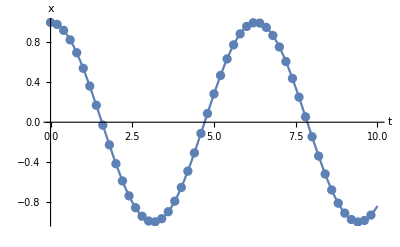

```mathematica
n=5*10;δt=2*10^-1;
f[t_,x_]:={x[[2]],-x[[1]]};
x0={1,0};data={x0};
Do[
k1=δt f[i δt,data[[-1]]];
k2=δt f[i δt+1/2 δt,data[[-1]]+k1/2];
k3=δt f[i δt+1/2 δt,data[[-1]]+k2/2];
k4=δt f[i δt+δt,data[[-1]]+k3];
AppendTo[data,data[[-1]]+1/6(k1+2k2+2k3+k4)],{i,n}]
(*data[[_,1]]为x数据，data[[_,2]]为x'数据*)
data=Table[{(i-1) δt,data[[i,1]]},{i,n}];
g1=ListPlot[data];
g2=Plot[Cos[t],{t,0,n δt},PlotRange->All];
Show[{g1,g2},AxesLabel->{"t","x"},PlotRange->All]
Clear["Global`*"]
```

边值问题

要求方程的解满足某些条件;
即不仅要求出函数本身，而且同时求出方程某些参数的值

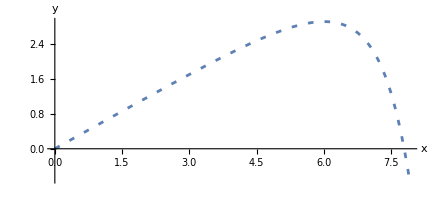

```mathematica
(*例如求炮弹仰角*)
v0=100;g=9.8;θ=π/6;η=0.5;time=1.5;
equs={x''[t]==-η √(x'[t]^2+y[t]^2) x'[t],
y''[t]==-g-η √(x'[t]^2+y[t]^2) y'[t],
x[0]==0,y[0]==0,x'[0]==v0 Cos[θ],y'[0]==v0 Sin[θ]};
s=NDSolve[equs,{x,y},{t,0,time}];
ParametricPlot[{x[t],y[t]}/.s[[1]],{t,0,time},AxesLabel->{"x","y"},PlotStyle->{Thickness[0.005],Dashing[{0.01,0.02}]}]
Clear["Global`*"]
```

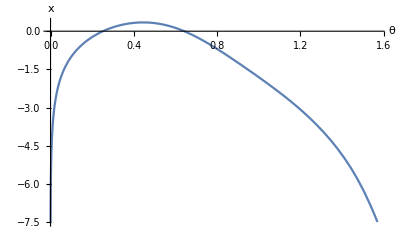

{0.251736,0.642211}

0.25π, 0.64π

When θ=0.445049 the max of x is 7.84458

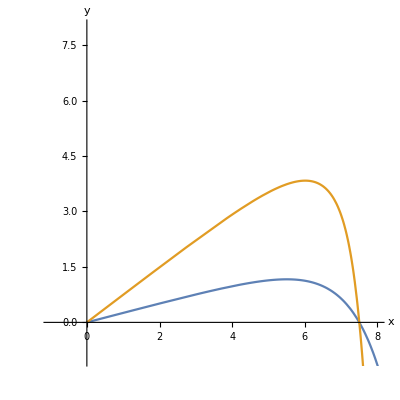

```mathematica
(*现在问当落点为7.5时，θ为多少？*)
v0=100;g=9.8;η=0.5;time=15;ϵ=10^-6;x0=7.5;
xx[θ_?NumberQ]:=
Block[{x,y,t,s},
Last[{s=NDSolve[{x''[t]==-η √(x'[t]^2+y[t]^2) x'[t],
y''[t]==-g-η √(x'[t]^2+y[t]^2) y'[t],
x[0]==0,y[0]==0,x'[0]==v0 Cos[θ],y'[0]==v0 Sin[θ]},{x,y},{t,0,time}];fun=y/.s[[1,2]];
ss=FindRoot[fun[t],{t,0+ϵ,time}];x[t/.ss[[1]]]/.s[[1,1]]}]];
Plot[xx[θ]-x0,{θ,ϵ,π/2},AxesLabel->{"θ","x"}]

θs=θ/.
{FindRoot[xx[θ]-x0,{θ,0,0.5}],
FindRoot[xx[θ]-x0,{θ,0.5,1}]}
Print[NumberForm[θs[[1]],2],"π, ",NumberForm[θs[[2]],2],"π"]

ss=FindMaximum[xx[θ],{θ,0.2,0.7}];
Print["When θ=",θ/.ss[[2,1]]," the max of x is ",ss[[1]]]
sols=Table[Last[{s=NDSolve[{x''[t]==-η √(x'[t]^2+y[t]^2) x'[t],
y''[t]==-g-η √(x'[t]^2+y[t]^2) y'[t],
x[0]==0,y[0]==0,x'[0]==v0 Cos[θ],y'[0]==v0 Sin[θ]},{x,y},{t,0,time}],{x[t]/.s[[1,1]],y[t]/.s[[1,2]]}}],{θ,θs}];
ParametricPlot[sols,{t,0,time},AxesLabel->{"x","y"},PlotRange->{-1,8}]
Clear["Global`*"]
```

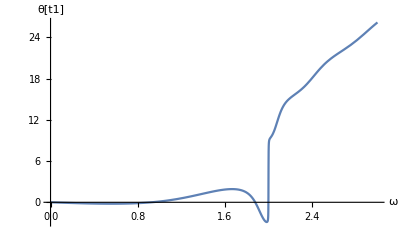

{0.924845,1.87817,1.99927}

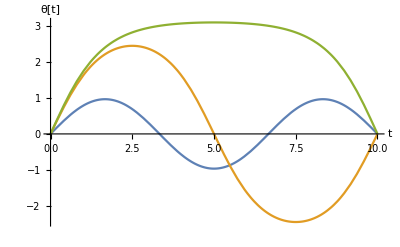

```mathematica
(*理想单摆，当t=0时，θ=0;当t=10时，θ=0，求初始角速度*)
t0=0;t1=10;
f[ω_?NumberQ]:=Block[{θ,t},First[θ[t1]/.NDSolve[{θ''[t]+Sin[θ[t]]==0,θ[t0]==0,θ'[t0]==ω},θ,{t,t0,t1}]]];
(*NDSolve[...]得到一个插值函数{{θ->InterpolatingFunction[...]}}(注意ω为形式变量，并且延迟赋值)θ[t1]/.{{θ->InterpolatingFunction[...]}}得到{θ[t1]}
	First[{θ[t1]}]得到θ[t1]*)
Plot[f[ω],{ω,0,3},AxesLabel->{"ω","θ[t1]"}]
ωs=ω/.
{FindRoot[f[ω],{ω,0.5,1}],
FindRoot[f[ω],{ω,1.5,1.9}],
FindRoot[f[ω],{ω,1.9,2.1}]}
sols=Table[First[θ[t]/.
NDSolve[{θ''[t]+Sin[θ[t]]==0,θ[t0]==0,θ'[t0]==ω},θ,{t,t0,t1}]],{ω,ωs}];
Plot[sols,{t,t0,t1},AxesLabel->{"t","θ[t]"}]
Clear["Global`*"]
```

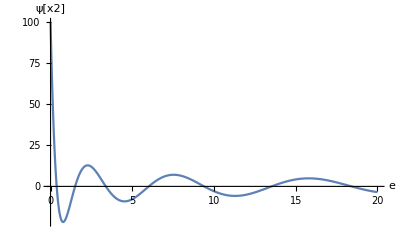

{0.37568,1.50272,3.38112,6.01088,9.392,13.5245,18.4083}

{1.,4.,9.,16.,25.,36.,49.}

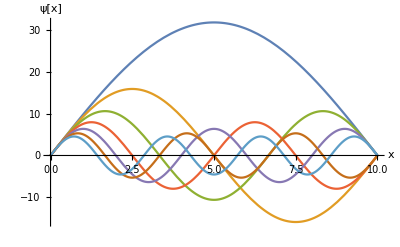

```mathematica
(*求量子力学一维无限深方势阱及本征值*)
x1=0;x2=10;β=0.262713;
f[e_?NumberQ]:=
Block[{ψ,x},
First[ψ[x2]/.NDSolve[{ψ''[x]+β e ψ[x]==0,ψ[x1]==0,ψ '[x1]==10},ψ,{x,x1,x2}]]]
(*不设定ψ[x2]==0,而任意设置ψ'[x1]的值，是为了防止得到平庸解*)
Plot[f[e],{e,0,20},AxesLabel->{"e","ψ[x2]"},PlotRange->All]
(*能量本征值*)
es=e/.
{FindRoot[f[e],{e,0,1}],
FindRoot[f[e],{e,1,2}],
FindRoot[f[e],{e,3,4}],
FindRoot[f[e],{e,5,7}],
FindRoot[f[e],{e,7,10}],
FindRoot[f[e],{e,10,15}],
FindRoot[f[e],{e,15,20}]}
(*能量本征值除以第一本征值*)
Table[es[[i]]/es[[1]],{i,Length[es]}]
sols=Table[First[ψ[x]/.
NDSolve[{ψ''[x]+β e ψ[x]==0,ψ[x1]==0,ψ'[x1]==10},ψ,{x,x1,x2}]],{e,es}];
Plot[sols,{x,x1,x2},AxesLabel->{"x","ψ[x]"}]
Clear["Global`*"]
```

## 5、求解偏微分方程

### 1、抛物型方程

```mathematica
(*抛物型方程一般形式:(∂u)/(∂t)==α(∂^2 u)/(∂x^2)*)
```

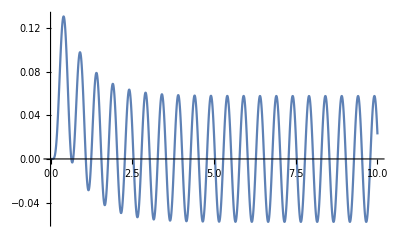

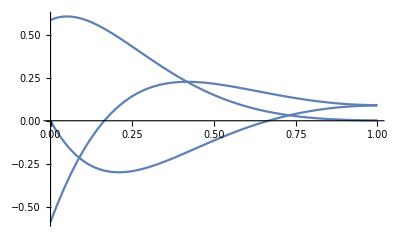

-Graphics3D-

```mathematica
L=1.0;α=0.5;
ss=NDSolve[{D[u[t,x],t]==α D[D[u[t,x],x],x],u[t,0]==Sin[4π t],u[0,x]==0,Derivative[0,1][u][t,L]==0},u,{x,0,L},{t,0,10}];
Plot[u[t,L]/.ss[[1]],{t,0,10}]
Plot[{u[0.3,x],u[0.5,x],u[0.7,x]}/.ss[[1]],{x,0,L}]
Plot3D[u[t,x]/.ss,{x,0,1},{t,0,10}]
Clear["Global`*"]
```

### 2、双曲型方程

```mathematica
(*双曲型方程一般形式:(∂^2 u)/(∂t^2)==α(∂^2 u)/(∂x^2)*)
```

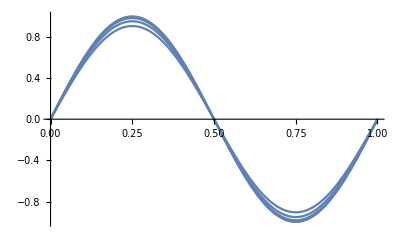

-Graphics3D-

```mathematica
L=1.0;T=0.1;
equ={D[u[t,x],{x,2}]-D[u[t,x],{t,2}]==0,u[0,x]==Sin[(2π x)/L],(D[u[t,x],t]/.t->0)==0,u[t,0]==0,u[t,L]==0};
ss=NDSolve[equ,u,{x,0,L},{t,0,T}];
Plot[{u[0.01,x],u[0.03,x],u[0.05,x],u[0.07,x]}/.ss[[1]],{x,0,L}]
Plot3D[u[t,x]/.ss,{x,0,1},{t,0,T}]
Clear["Global`*"]
```

## 更多细节

### 1、差分公式

设函数u = u[t, x], 其中t表示时间, x表示空间坐标.
在连续时空中取一些分立的点,均匀分布.
t_i=i×δt i=0,1,2,...
x_j=j×δx j=0,1,2,...
用u_(i,j)表示u(iδt,jδt)
将(∂u)/(∂x)离散化
向前差分公式
(u_(i,j))_x=(u_(i,j+1)-u_(i,j))/δx
向后差分公式
(u_(i,j))_x=(u_(i,j)-u_(i,j-1))/δx
中心差分公式
(u_(i,j))_x=(u_(i,j+1)-u_(i,j-1))/(2δx)
二阶偏导数的中心差分公式
(u_(i,j))_xx=(u_(i,j+1)-2 u_(i,j)+u_(i,j-1))/δx^2

### 2、抛物型方程

#### 1)四点格式

u_t=α u_xx,u[t,0]=sin[4π t],u[0,x]=0,u_x[t,L]=0
这个模型的完整表述如上,
模型-1的数值解如下进行:
空间二阶偏导数用中心差分表示:
(u_(i,j))_xx=(u_(i,j+1)-2 u_(i,j)+u_(i,j-1))/δx^2
时间的一阶偏导数采用后差分公式:
(u_(i,j))_t=(u_(i,j)-u_(i-1,j))/δt
于是热传导方程编程如下差分方程:
α(u_(i,j+1)-2 u_(i,j)+u_(i,j-1))/δx^2=(u_(i,j)-u_(i-1,j))/δt
整理上式，得到"四点格式"差分方程
u_(i,j-1)-(2+ρ)u_(i,j)+u_(i,j+1)=-ρ u_(i-1,j)
其中i,j=1,2,...; 而ρ=δx^2/(α δt)
对于初始条件,可以写成
u_(0,j)=0,j=0,1,2...
对于左边界条件,可以写作
u_(i,0)=Sin[4π×i×δ],i=0,1,2...
对于右边界条件,考虑热传导方程的差分形式,可以写作
(u_(i,n))_x=(u_(i,n+1)-u_(i,n-1))/(2δx)=0,δx=L/n
即为,2 u_(i,n-1)-(2+ρ)u_(i,n)=-ρ u_(i-1,n),ρ=δx^2/(α δt)
于是我们有方程组的如下:
Piecewise[{{u_(i,j-1)-(2+ρ)u_(i,j)+u_(i,j+1)=-ρ u_(i-1,j), i,j=1,2,...}, {u_(0,j)=0, j=0,1,2...}, {u_(i,0)=Sin[4π×i×δ], i=0,1,2...}, {2 u_(i,n-1)-(2+ρ)u_(i,n)=-ρ u_(i-1,n), ρ=δx^2/(α δt),i=0,1,2...}}]

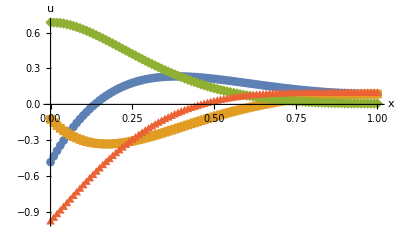

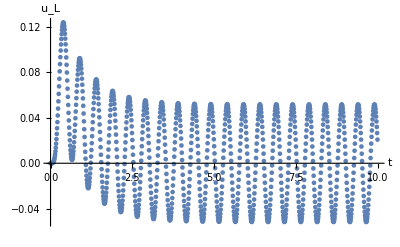

```mathematica
(*我们需要有五组变量;
data中保存各个时刻u随x变化的离散数据;
X中保存各个分点的x值;
Subscript[U, 0] 中保存各个x的分点上u的表示符号u[i],但是不含边界;
U是把x=0 Subscript[的u值添加到U, 0] 开头后完整的列表;
Lu中保存各个时刻的x=L处的u值*)
L=1.0;n=10^2;m=10^3;
δx=L/n;δt=10^-2;α=0.5;ρ=δx^2/(α δt);
f[t_]:=Sin[4π t];X=Table[i δx,{i,0,n}];
data={};Lu={{0,0}};
AppendTo[data,{0 δt,Table[{i δx,0},{i,0,n}]}];
(*data中存放着{{0时刻,{所有{x格点坐标(从0到n),0时刻}}}}*)
U0=Array[u,n];
(*U0中存放着{u[1],u[2],...,u[n]}*)
Do[
U=Prepend[U0,f[(j-1)δt]];
(*U中存放着j-1(从1到m-1)时刻的{(左边界条件)u[0](数值),u[1](变量),...,u[n](变量)}*)
equs=Table[
U[[i-1]]-(2+ρ)U[[i]]+U[[i+1]]==-ρ data[[-1,2]][[i,2]],
(*j-1时刻时候的四点格式差分方程,其中data[[-1,2]][[i,2]]为j-2时刻的u*)
{i,2,n}];
(*equs中为j-1时刻时候的四点格式差分方程组,,其中data[[-1,2]][[i,2]]为j-2时刻的*)
AppendTo[
	equs,2U[[n]]-(2+ρ)U[[n+1]]==-ρ data[[-1,2]][[n+1,2]]];
(*equs中添加为j-1时刻时候的右边界条件,data[[-1,2]][[n+1,2]]为u[n]*)
s=Solve[equs,U0];
(*s为在j-1时刻u的解的替换规则(诸如{u[1]-> xxx,u[2]->xxx,...}})*)
u=U/.s[[1]];
(*将u赋值为j-1时刻的u的解{u[1],u[2],...,u[n]}*)
AppendTo[Lu,{(j-1)δt,u[[-1]]}];
(*将Lu添加j-1时刻的{j-1时刻,u[n]}*)
u={X,u}ᵀ;
(*注意转置输入为Esc tr Esc,而非Ctrl-6 T*)
(*u变为{{{{{格点0, 时刻j-1的u[0]}}}, {{{格点1, 时刻j-1的u[1]}, {..., ...}}}}}或{{格点0,u[0]},{格点1,u[1]},...}*)
AppendTo[data,{(j-1)δt,u}],{j,2,m}]
(*data中数据为{{时刻0,{{格点0,u[0]},{格点1,u[1]},...}},{时刻1,{{格点0,u[0]},...}}...}*)
(*data[[30,2]]为时刻30时的格点和u,即{{格点0,u[0]},{格点1,u[1]},...}}*)
ListPlot[{data[[30,2]],data[[50,2]],data[[70,2]],data[[90,2]]},
PlotMarkers->Automatic,AxesLabel->{"x","u"},PlotRange->All]
(*Lu为不同时刻的u[n],即为{{时刻0,u[n]},{时刻1,u[n]},...}*)
ListPlot[Lu,AxesLabel->{"t","u_L"}]
Clear["Global`*"]
```

#### 2)六点格式

(1)将热传导方程在时刻t^*=i×δt-δt/2 的地方进行中心差分;
(2)将t^*时刻的u^*用相邻两个时刻的平均值代替,
u^*=1/2(u_(i,j)-u_(i-1,j))
得到差分方程
u_(i,j-1)-2(1+ρ)u_(i,j)+u_(i,j+1)=-u_(i-1,j-1)-2(ρ-1)u_(i-1,j)-u_(i-1,j+1)
而边界值的处理没有改变.

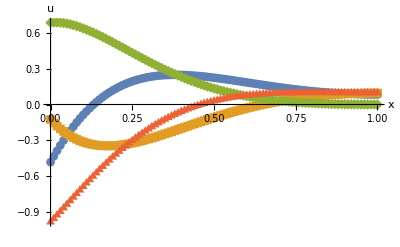

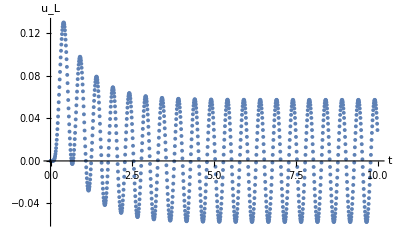

```mathematica
(*我们需要有五组变量;
data中保存各个时刻u随x变化的离散数据;
X中保存各个分点的x值;
Subscript[U, 0] 中保存各个x的分点上u的表示符号u[i],但是不含边界;
U是把x=0 Subscript[的u值添加到U, 0] 开头后完整的列表;
Lu中保存各个时刻的x=L处的u值*)
L=1.0;n=10^2;m=10^3;
δx=L/n;δt=10^-2;α=0.5;ρ=δx^2/(α δt);
f[t_]:=Sin[4π t];X=Table[i δx,{i,0,n}];
data={};Lu={{0,0}};
AppendTo[data,{0 δt,Table[{i δx,0},{i,0,n}]}];
(*data中存放着{{0时刻,{所有{x格点坐标(从0到n),0时刻}}}}*)
U0=Array[u,n];
(*U0中存放着{u[1],u[2],...,u[n]}*)
Do[
U=Prepend[U0,f[(j-1)δt]];
(*U中存放着j-1(从1到m-1)时刻的{(左边界条件)u[0](数值),u[1](变量),...,u[n](变量)}*)
equs=Table[
U[[i-1]]-2(1+ρ)U[[i]]+U[[i+1]]==- data[[-1,2]][[i-1,2]]-2(ρ-1)data[[-1,2]][[i,2]]-data[[-1,2]][[i+1,2]],
(*j-1时刻时候的四点格式差分方程,其中data[[-1,2]][[i,2]]为j-2时刻的u*)
{i,2,n}];
(*equs中为j-1时刻时候的四点格式差分方程组,,其中data[[-1,2]][[i,2]]为j-2时刻的*)
AppendTo[
	equs,2U[[n]]-(2+ρ)U[[n+1]]==-ρ data[[-1,2]][[n+1,2]]];
(*equs中添加为j-1时刻时候的右边界条件,data[[-1,2]][[n+1,2]]为u[n]*)
s=Solve[equs,U0];
(*s为在j-1时刻u的解的替换规则(诸如{u[1]-> xxx,u[2]->xxx,...}})*)
u=U/.s[[1]];
(*将u赋值为j-1时刻的u的解{u[1],u[2],...,u[n]}*)
AppendTo[Lu,{(j-1)δt,u[[-1]]}];
(*将Lu添加j-1时刻的{j-1时刻,u[n]}*)
u={X,u}ᵀ;
(*注意转置输入为Esc tr Esc,而非Ctrl-6 T*)
(*u变为{{{{{格点0, 时刻j-1的u[0]}}}, {{{格点1, 时刻j-1的u[1]}, {..., ...}}}}}或{{格点0,u[0]},{格点1,u[1]},...}*)
AppendTo[data,{(j-1)δt,u}],{j,2,m}]
(*data中数据为{{时刻0,{{格点0,u[0]},{格点1,u[1]},...}},{时刻1,{{格点0,u[0]},...}}...}*)
(*data[[30,2]]为时刻30时的格点和u,即{{格点0,u[0]},{格点1,u[1]},...}}*)
ListPlot[{data[[30,2]],data[[50,2]],data[[70,2]],data[[90,2]]},
PlotMarkers->Automatic,AxesLabel->{"x","u"},PlotRange->All]
(*Lu为不同时刻的u[n],即为{{时刻0,u[n]},{时刻1,u[n]},...}*)
ListPlot[Lu,AxesLabel->{"t","u_L"}]
Clear["Global`*"]
```

### 3、双曲型方程

```mathematica
(*双曲型方程一般形式:(∂^2 u)/(∂t^2)==α(∂^2 u)/(∂x^2)*)
```

u_xx-u_tt==0;
u[0,x]==Sin[(2π x)/L],u_t[0,x]==0;(*初始条件*)
u[t,0]==u[t,L]==0;(*边值条件*)
由于u=u[t,x]对于坐标和时间都是二阶偏导数,对这两个二阶偏导数采取中心差分格式
u_(i+1,j)==ρ u_(i,j+1)+2(1-ρ)u_(i,j)+ρ u_(i,j-1)-u_(i-1,j)
其中,ρ=δt^2/δx^2;
即为计算i+1时刻的u,需要i时刻和i-1时刻的u;
但是t=0时刻的u分布给定了,
而t=1时刻的则由 初始条件差分 和 边值条件 得到
(u_(1,j)-u_(0,j))/δt==0 
故
	u_(1,j)=u_(0,j)=Sin[(2 π j δx)/L].
进而得到 所有时刻 和 位置 的u值.

#### 改进

假设在t=0之前还有一时刻,把t=0作为中心差分点,则有
u_(1,j)==ρ u_(0,j+1)+2(1-ρ)u_(0,j)+ρ u_(0,j-1)-u_(-1,j)
但是u_(-1,j)并没有给出,为消除假点,可以将u_t[0,x]==0采用中心差分
(u_(1,j)-u_(-1,j))/(2 δt)==0
故有u_(-1,j)==u_(1,j)
带入之前差分方程得到
u_(1,j)==(ρ (u_(0,j+1)+u_(0,j-1)))/2+(1-ρ)u_(0,j)
以及
u_(i+1,j)==ρ u_(i,j+1)+2(1-ρ)u_(i,j)+ρ u_(i,j-1)-u_(i-1,j)
u的精度提高一阶

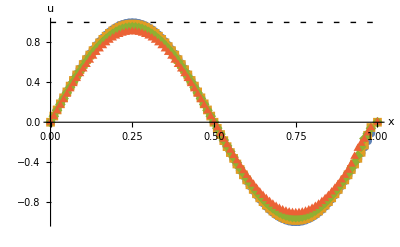

```mathematica
L=1.0;n=10^2;m=10^2;
δx=L/n;δt=10^-3;ρ=(δt/δx)^2;
f[x_]:=Sin[(2π x)/L];
u0=un=0;data={};
AppendTo[data,{0 δt,Table[{i δx,f[i δx]},{i,0,n}]}];
(*data中存放着{{0时刻,{所有{x格点坐标(从0到n),0时刻的u[x]}}}}*)
u=Table[
{i δx,ρ/2(f[i δx +δx]+f[i δx-δx])+(1-ρ)f[i δx]},{i,n-1}];
(*u中存放着1时刻,由中心差分得到的{{δx,u[1]},{2δx,u[2]},...{坐标,u值}...,{(n-1)δx,u[n-1]}}*)
PrependTo[u,{0,u0}];AppendTo[u,{L,un}];
AppendTo[data,{δt,u}];
Do[
u=Table[{(i-1) δx,ρ data[[j-1,2]][[i+1,2]]+2(1-ρ)data[[j-1,2]][[i,2]]+ρ data[[j-1,2]][[i-1,2]]-data[[j-2,2]][[i,2]]},{i,2,n-1}];
(*u中存放着j时刻,i-1(从1到n-2)坐标的{{0 δx,u[0]},{δx,u[1]},...{坐标,u[坐标]}...}*)
PrependTo[u,{0,u0}];AppendTo[u,{L,un}];
AppendTo[data,{(j-1) δt,u}],
(*data中数据为{{时刻0,{{格点0,u[0]},{格点1,u[1]},...}},{时刻1,{{格点0,u[0]},...}}...}*)
{j,3,m}]
(*data[[30,2]]为时刻30时的格点和u,即{{格点0,u[0]},{格点1,u[1]},...}}*)
ListPlot[{data[[10,2]],data[[30,2]],data[[50,2]],data[[70,2]]},
PlotMarkers->Automatic,AxesLabel->{"x","u"},PlotRange->{All,{-1,1}},Epilog->{Dashing[{0.01,0.02}],Line[{{0,1},{L,1}}]}]
(*Lu为不同时刻的u[n],即为{{时刻0,u[n]},{时刻1,u[n]},...}*)
Clear["Global`*"]
```

## 6、求解本征值问题